# Cost of Dai Collateral Attack

```mathematica
LiquidationThreshold = 1.5;
DaiCirculation =77000000;
EthCollateral = 355000000;
KeeperDiscount = 0.03;
AvgTxPrice = 0.20;
CDPOpenNumTx =2;
CDPClosingNumTx = 6;
PETHEx = 1.04;
```

## Decrease overall collateral ratio (simple)

```mathematica
cost[target_, CDPratio_] = (EthCollateral - target * DaiCirculation) / (target - CDPratio);
```

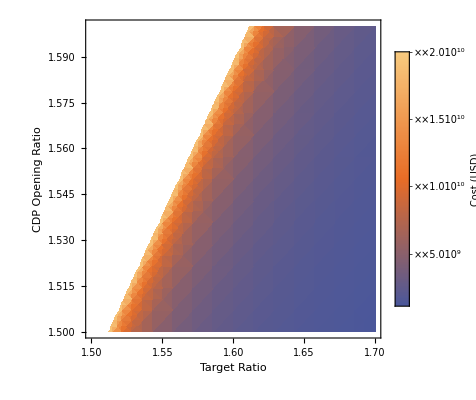

```mathematica
DensityPlot[cost[t,r],{t,1.5,1.7}, {r,1.5,1.6},FrameLabel->{"Target Ratio", "CDP Opening Ratio"}, PlotLegends-> BarLegend[Automatic, LegendLabel->"Cost (USD)"], PlotRange->{0,2*10^10}, PlotTheme->"Scientific"]
```

## Decrease overall collateral ratio (including tx cost)